# ANN Simulation

This is done only for the cross evaluation, as it is the most useful

## Importing Data

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/ff278/Desktop/Previous_Lutein/Current/Lutein_Experiment

```mathematica
(*Type 1 Network*)
(*Against set 1,2 4*)
(*For Test cases  the Rows are in order, from left to right
Index (1)
Illumination DCW nitrate lutein for the experimental data (2,3,4,5)
Illumination DCW nitrate lutein for the 12 step (6,7,8,9)
Illumination DCW nitrate lutein for the 24 step (10,11,12,13)
Illumination DCW nitrate lutein for the 36 step (14,15,16,17)
Illumination DCW nitrate lutein for the 72 step (18,19,20,21)*
From left to Right they are set 1, 2 and 4*)
```

```mathematica
(*Lutein thus is index 5,9,13,17,21*)
```

```mathematica
IntervalsLength={{0,12,24,36,48,60,72,84,96,108,120,132},{0,24,48,72,96,120,144},{0,36,72,108,144},{0,72,144}}
{{0,12,24,36,48,60,72,84,96,108,120,132,144},{0,24,48,72,96,120,144},{0,36,72,108,144},{0,72,144}}
(*Type 2 Network*)
(*Against set 1,2 4*)
(*For Test cases  the rows are in order, from up to down
Illumination DCW nitrate lutein for the experimental data (2,3,4,5)
Illumination DCW nitrate lutein for the simulated data (6,7,8,9)*
From up to down they are set 1, 2 and 4.
Lutein is 5 and 9*)

lutInd2={5,10}
nitInd2={4,9}
DCWInd2={3,8}
```

{{0,12,24,36,48,60,72,84,96,108,120,132},{0,24,48,72,96,120,144},{0,36,72,108,144},{0,72,144}}

{{0,12,24,36,48,60,72,84,96,108,120,132,144},{0,24,48,72,96,120,144},{0,36,72,108,144},{0,72,144}}

{5,10}

{4,9}

{3,8}

```mathematica
ValT2H1Cross=DeleteCases[Import["data/Lutein_NN_Type2H1_Training_LessNoise2_SimTrajSTD_Rescale.csv","CSV"][[3;;]]//Transpose,"",-1];
LUTEIN1A=Part[ValT2H1Cross,lutInd2];
NIT1A=Part[ValT2H1Cross,nitInd2];
DCW1A=Part[ValT2H1Cross,DCWInd2];
```

```mathematica
Length[DCW1A[[2]]]
```

60

```mathematica
(*The two cross validation sets*)
```

```mathematica
RealLut1=LUTEIN1A[[1]][[;;12]];
RealNit1=NIT1A[[1]][[;;12]];
RealDCW1=DCW1A[[1]][[;;12]];
RealLut2=LUTEIN1A[[1]][[13;;24]];
RealNit2=NIT1A[[1]][[13;;24]];
RealDCW2=DCW1A[[1]][[13;;24]];
RealLut3=LUTEIN1A[[1]][[25;;36]];
RealNit3=NIT1A[[1]][[25;;36]];
RealDCW3=DCW1A[[1]][[25;;36]];
RealLut4=LUTEIN1A[[1]][[37;;48]];
RealNit4=NIT1A[[1]][[37;;48]];
RealDCW4=DCW1A[[1]][[37;;48]];
RealLut5=LUTEIN1A[[1]][[49;;60]];
RealNit5=NIT1A[[1]][[49;;60]];
RealDCW5=DCW1A[[1]][[49;;60]];
```

```mathematica
LUTEINA1=LUTEIN1A[[2]][[;;12]];
NITA1=NIT1A[[2]][[;;12]];
DCWA1=DCW1A[[2]][[;;12]];
LUTEINB1=LUTEIN1A[[2]][[13;;24]];
NITB1=NIT1A[[2]][[13;;24]];
DCWB1=DCW1A[[2]][[13;;24]];
LUTEINC1=LUTEIN1A[[2]][[25;;36]];
NITC1=NIT1A[[2]][[25;;36]];
DCWC1=DCW1A[[2]][[25;;36]];
LUTEIND1=LUTEIN1A[[2]][[37;;48]];
NITD1=NIT1A[[2]][[37;;48]];
DCWD1=DCW1A[[2]][[37;;48]];
LUTEINE1=LUTEIN1A[[2]][[49;;60]];
NITE1=NIT1A[[2]][[49;;60]];
DCWE1=DCW1A[[2]][[49;;60]];
```

```mathematica
RealLutA1=Table[{IntervalsLength[[1,i]],RealLut1[[i]]},{i,Length[IntervalsLength[[1]]]}];
RealNitA1=Table[{IntervalsLength[[1,i]],RealNit1[[i]]},{i,Length[IntervalsLength[[1]]]}];
RealDCWA1=Table[{IntervalsLength[[1,i]],RealDCW1[[i]]},{i,Length[IntervalsLength[[1]]]}];

RealLutB1=Table[{IntervalsLength[[1,i]],RealLut2[[i]]},{i,Length[IntervalsLength[[1]]]}];
RealNitB1=Table[{IntervalsLength[[1,i]],RealNit2[[i]]},{i,Length[IntervalsLength[[1]]]}];
RealDCWB1=Table[{IntervalsLength[[1,i]],RealDCW2[[i]]},{i,Length[IntervalsLength[[1]]]}];

RealLutC1=Table[{IntervalsLength[[1,i]],RealLut3[[i]]},{i,Length[IntervalsLength[[1]]]}];
RealNitC1=Table[{IntervalsLength[[1,i]],RealNit3[[i]]},{i,Length[IntervalsLength[[1]]]}];
RealDCWC1=Table[{IntervalsLength[[1,i]],RealDCW3[[i]]},{i,Length[IntervalsLength[[1]]]}];

RealLutD1=Table[{IntervalsLength[[1,i]],RealLut4[[i]]},{i,Length[IntervalsLength[[1]]]}];
RealNitD1=Table[{IntervalsLength[[1,i]],RealNit4[[i]]},{i,Length[IntervalsLength[[1]]]}];
RealDCWD1=Table[{IntervalsLength[[1,i]],RealDCW4[[i]]},{i,Length[IntervalsLength[[1]]]}];

RealLutE1=Table[{IntervalsLength[[1,i]],RealLut5[[i]]},{i,Length[IntervalsLength[[1]]]}];
RealNitE1=Table[{IntervalsLength[[1,i]],RealNit5[[i]]},{i,Length[IntervalsLength[[1]]]}];
RealDCWE1=Table[{IntervalsLength[[1,i]],RealDCW5[[i]]},{i,Length[IntervalsLength[[1]]]}];
```

```mathematica
CROSSLUT1A=Table[{IntervalsLength[[1,i]],LUTEINA1[[i]]},{i,Length[IntervalsLength[[1]]]}];
CROSSNIT1A=Table[{IntervalsLength[[1,i]],NITA1[[i]]},{i,Length[IntervalsLength[[1]]]}];
CROSSDCW1A=Table[{IntervalsLength[[1,i]],DCWA1[[i]]},{i,Length[IntervalsLength[[1]]]}];

CROSSLUT1B=Table[{IntervalsLength[[1,i]],LUTEINB1[[i]]},{i,Length[IntervalsLength[[1]]]}];
CROSSNIT1B=Table[{IntervalsLength[[1,i]],NITB1[[i]]},{i,Length[IntervalsLength[[1]]]}];
CROSSDCW1B=Table[{IntervalsLength[[1,i]],DCWB1[[i]]},{i,Length[IntervalsLength[[1]]]}];

CROSSLUT1C=Table[{IntervalsLength[[1,i]],LUTEINC1[[i]]},{i,Length[IntervalsLength[[1]]]}];
CROSSNIT1C=Table[{IntervalsLength[[1,i]],NITC1[[i]]},{i,Length[IntervalsLength[[1]]]}];
CROSSDCW1C=Table[{IntervalsLength[[1,i]],DCWC1[[i]]},{i,Length[IntervalsLength[[1]]]}];

CROSSLUT1D=Table[{IntervalsLength[[1,i]],LUTEIND1[[i]]},{i,Length[IntervalsLength[[1]]]}];
CROSSNIT1D=Table[{IntervalsLength[[1,i]],NITD1[[i]]},{i,Length[IntervalsLength[[1]]]}];
CROSSDCW1D=Table[{IntervalsLength[[1,i]],DCWD1[[i]]},{i,Length[IntervalsLength[[1]]]}];

CROSSLUT1E=Table[{IntervalsLength[[1,i]],LUTEINE1[[i]]},{i,Length[IntervalsLength[[1]]]}];
CROSSNIT1E=Table[{IntervalsLength[[1,i]],NITE1[[i]]},{i,Length[IntervalsLength[[1]]]}];
CROSSDCW1E=Table[{IntervalsLength[[1,i]],DCWE1[[i]]},{i,Length[IntervalsLength[[1]]]}];
```

```mathematica
ValT2H2CrossVal=DeleteCases[Import["data/Lutein_NN_Type2H2_Training_LessNoise2_SimTrajSTD_Rescale.csv","CSV"][[3;;]]//Transpose,"",-1];
LUTEIN8A=Part[ValT2H2CrossVal,lutInd2][[2]];
NIT8A=Part[ValT2H2CrossVal,nitInd2][[2]];
DCW8A=Part[ValT2H2CrossVal,DCWInd2][[2]];
```

```mathematica
LUTEIN8A//Length
```

60

```mathematica
LUTEINA8=LUTEIN8A[[;;12]];
NITA8=NIT8A[[;;12]];
DCWA8=DCW8A[[;;12]];
LUTEINB8=LUTEIN8A[[13;;24]];
NITB8=NIT8A[[13;;24]];
DCWB8=DCW8A[[13;;24]];
LUTEINC8=LUTEIN8A[[25;;36]];
NITC8=NIT8A[[25;;36]];
DCWC8=DCW8A[[25;;36]];
LUTEIND8=LUTEIN8A[[37;;48]];
NITD8=NIT8A[[37;;48]];
DCWD8=DCW8A[[37;;48]];
LUTEINE8=LUTEIN8A[[49;;60]];
NITE8=NIT8A[[49;;60]];
DCWE8=DCW8A[[49;;60]];
```

```mathematica
CROSSLUT8A=Table[{IntervalsLength[[1,i]],LUTEINA8[[i]]},{i,Length[IntervalsLength[[1]]]}];
CROSSNIT8A=Table[{IntervalsLength[[1,i]],NITA8[[i]]},{i,Length[IntervalsLength[[1]]]}];
CROSSDCW8A=Table[{IntervalsLength[[1,i]],DCWA8[[i]]},{i,Length[IntervalsLength[[1]]]}];

CROSSLUT8B=Table[{IntervalsLength[[1,i]],LUTEINB8[[i]]},{i,Length[IntervalsLength[[1]]]}];
CROSSNIT8B=Table[{IntervalsLength[[1,i]],NITB8[[i]]},{i,Length[IntervalsLength[[1]]]}];
CROSSDCW8B=Table[{IntervalsLength[[1,i]],DCWB8[[i]]},{i,Length[IntervalsLength[[1]]]}];

CROSSLUT8C=Table[{IntervalsLength[[1,i]],LUTEINC8[[i]]},{i,Length[IntervalsLength[[1]]]}];
CROSSNIT8C=Table[{IntervalsLength[[1,i]],NITC8[[i]]},{i,Length[IntervalsLength[[1]]]}];
CROSSDCW8C=Table[{IntervalsLength[[1,i]],DCWC8[[i]]},{i,Length[IntervalsLength[[1]]]}];

CROSSLUT8D=Table[{IntervalsLength[[1,i]],LUTEIND8[[i]]},{i,Length[IntervalsLength[[1]]]}];
CROSSNIT8D=Table[{IntervalsLength[[1,i]],NITD8[[i]]},{i,Length[IntervalsLength[[1]]]}];
CROSSDCW8D=Table[{IntervalsLength[[1,i]],DCWD8[[i]]},{i,Length[IntervalsLength[[1]]]}];

CROSSLUT8E=Table[{IntervalsLength[[1,i]],LUTEINE8[[i]]},{i,Length[IntervalsLength[[1]]]}];
CROSSNIT8E=Table[{IntervalsLength[[1,i]],NITE8[[i]]},{i,Length[IntervalsLength[[1]]]}];
CROSSDCW8E=Table[{IntervalsLength[[1,i]],DCWE8[[i]]},{i,Length[IntervalsLength[[1]]]}];
```

## Plotting Data

### Lutein

```mathematica
(*This is plotted in regard to the cross validation data*)
```

```mathematica
(*Type 1, 1 Layer*)
```

```mathematica
legendLab2={"Experimental","Simulated"}
```

{Experimental,Simulated}

```mathematica
axlal={"Time","Concentration"}
```

{Time,Concentration}

```mathematica
(*1 Hidden layer*)
```

```mathematica
(*Fully Simulated Trajectory*)
```

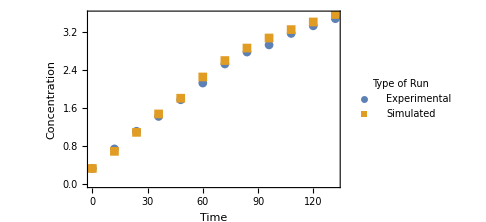

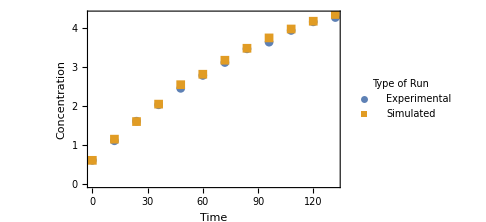

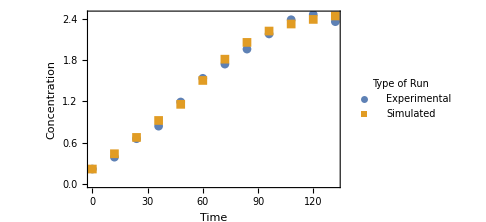

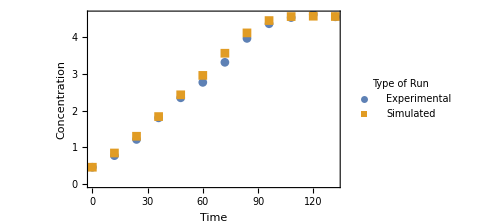

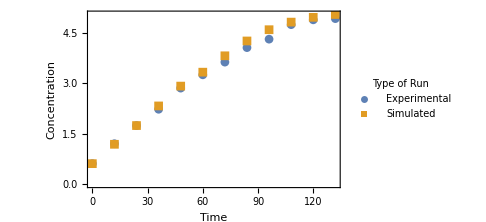

```mathematica
ListPlot[{RealLutA1,CROSSLUT1A},PlotMarkers->Automatic,Frame->True,FrameLabel->axlal,LabelStyle->Bold,PlotLegends->Placed[LineLegend[legendLab2,LegendLabel->"Type of Run",LegendFunction->(Framed[#,RoundingRadius->5]&),LabelStyle-> 10],{0.8,0.3}],ImageSize->Medium]
ListPlot[{RealLutB1,CROSSLUT1B},PlotMarkers->Automatic,Frame->True,FrameLabel->axlal,LabelStyle->Bold,PlotLegends->Placed[LineLegend[legendLab2,LegendLabel->"Type of Run",LegendFunction->(Framed[#,RoundingRadius->5]&),LabelStyle-> 10],{0.8,0.3}],ImageSize->Medium]
ListPlot[{RealLutC1,CROSSLUT1C},PlotMarkers->Automatic,Frame->True,FrameLabel->axlal,LabelStyle->Bold,PlotLegends->Placed[LineLegend[legendLab2,LegendLabel->"Type of Run",LegendFunction->(Framed[#,RoundingRadius->5]&),LabelStyle-> 10],{0.8,0.3}],ImageSize->Medium]
ListPlot[{RealLutD1,CROSSLUT1D},PlotMarkers->Automatic,Frame->True,FrameLabel->axlal,LabelStyle->Bold,PlotLegends->Placed[LineLegend[legendLab2,LegendLabel->"Type of Run",LegendFunction->(Framed[#,RoundingRadius->5]&),LabelStyle-> 10],{0.8,0.3}],ImageSize->Medium]
ListPlot[{RealLutE1,CROSSLUT1E},PlotMarkers->Automatic,Frame->True,FrameLabel->axlal,LabelStyle->Bold,PlotLegends->Placed[LineLegend[legendLab2,LegendLabel->"Type of Run",LegendFunction->(Framed[#,RoundingRadius->5]&),LabelStyle-> 10],{0.8,0.3}],ImageSize->Medium]
```

```mathematica
(*2 Hidden Layers*)
```

```mathematica
(*Fully Simulated Trajectory*)
```

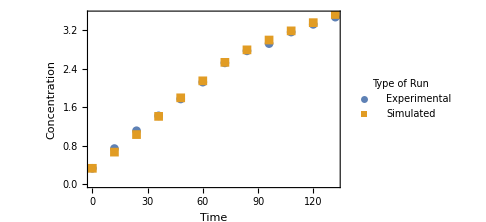

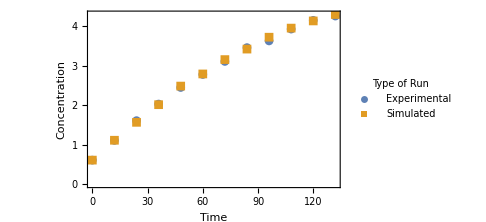

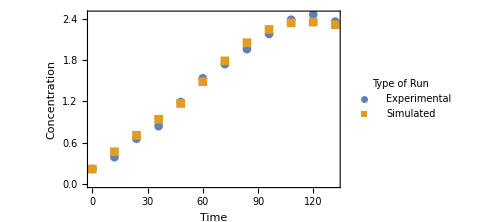

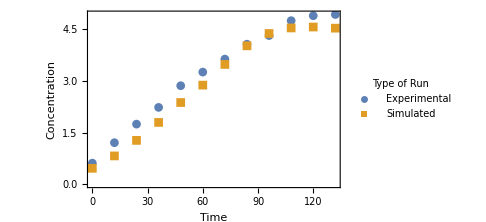

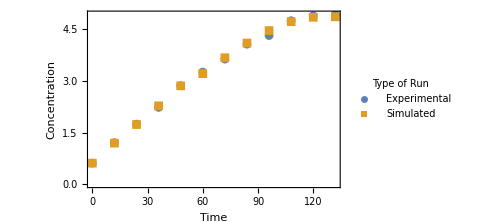

```mathematica
ListPlot[{RealLutA1,CROSSLUT8A},PlotMarkers->Automatic,Frame->True,FrameLabel->axlal,LabelStyle->Bold,PlotLegends->Placed[LineLegend[legendLab2,LegendLabel->"Type of Run",LegendFunction->(Framed[#,RoundingRadius->5]&),LabelStyle-> 10],{0.8,0.3}],ImageSize->Medium]
ListPlot[{RealLutB1,CROSSLUT8B},PlotMarkers->Automatic,Frame->True,FrameLabel->axlal,LabelStyle->Bold,PlotLegends->Placed[LineLegend[legendLab2,LegendLabel->"Type of Run",LegendFunction->(Framed[#,RoundingRadius->5]&),LabelStyle-> 10],{0.8,0.3}],ImageSize->Medium]
ListPlot[{RealLutC1,CROSSLUT8C},PlotMarkers->Automatic,Frame->True,FrameLabel->axlal,LabelStyle->Bold,PlotLegends->Placed[LineLegend[legendLab2,LegendLabel->"Type of Run",LegendFunction->(Framed[#,RoundingRadius->5]&),LabelStyle-> 10],{0.8,0.3}],ImageSize->Medium]
ListPlot[{RealLutE1,CROSSLUT8D},PlotMarkers->Automatic,Frame->True,FrameLabel->axlal,LabelStyle->Bold,PlotLegends->Placed[LineLegend[legendLab2,LegendLabel->"Type of Run",LegendFunction->(Framed[#,RoundingRadius->5]&),LabelStyle-> 10],{0.8,0.3}],ImageSize->Medium]
ListPlot[{RealLutE1,CROSSLUT8E},PlotMarkers->Automatic,Frame->True,FrameLabel->axlal,LabelStyle->Bold,PlotLegends->Placed[LineLegend[legendLab2,LegendLabel->"Type of Run",LegendFunction->(Framed[#,RoundingRadius->5]&),LabelStyle-> 10],{0.8,0.3}],ImageSize->Medium]
```

### Nitrogen

```mathematica
(*This is plotted in regard to the cross validation data*)
```

```mathematica
(*Type 1, 1 Layer*)
```

```mathematica
legendLab2={"Experimental","Simulated"}
```

{Experimental,Simulated}

```mathematica
(*1 Hidden layer*)
```

```mathematica
(*Expected value from experimental point*)
```

```mathematica
(*Fully Simulated Trajectory*)
```

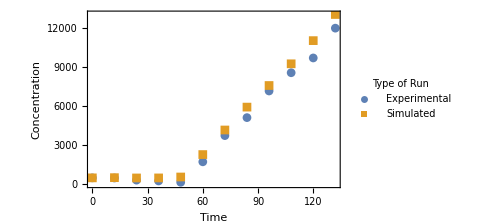

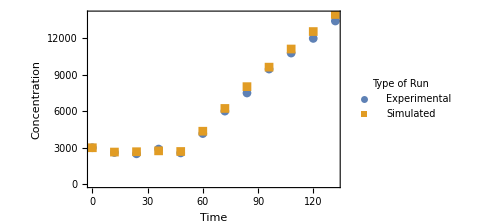

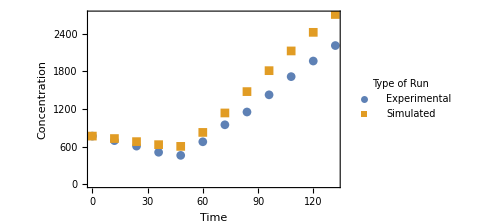

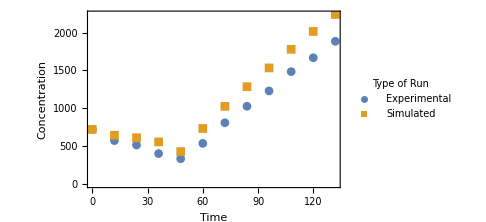

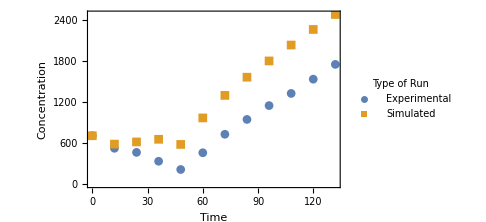

```mathematica
ListPlot[{RealNitA1,CROSSNIT1A},PlotMarkers->Automatic,Frame->True,FrameLabel->axlal,LabelStyle->Bold,PlotLegends->Placed[LineLegend[legendLab2,LegendLabel->"Type of Run",LegendFunction->(Framed[#,RoundingRadius->5]&),LabelStyle-> 10],{0.3,0.7}],ImageSize->Medium]
ListPlot[{RealNitB1,CROSSNIT1B},PlotMarkers->Automatic,Frame->True,FrameLabel->axlal,LabelStyle->Bold,PlotLegends->Placed[LineLegend[legendLab2,LegendLabel->"Type of Run",LegendFunction->(Framed[#,RoundingRadius->5]&),LabelStyle-> 10],{0.3,0.7}],ImageSize->Medium]
ListPlot[{RealNitC1,CROSSNIT1C},PlotMarkers->Automatic,Frame->True,FrameLabel->axlal,LabelStyle->Bold,PlotLegends->Placed[LineLegend[legendLab2,LegendLabel->"Type of Run",LegendFunction->(Framed[#,RoundingRadius->5]&),LabelStyle-> 10],{0.3,0.7}],ImageSize->Medium]
ListPlot[{RealNitD1,CROSSNIT1D},PlotMarkers->Automatic,Frame->True,FrameLabel->axlal,LabelStyle->Bold,PlotLegends->Placed[LineLegend[legendLab2,LegendLabel->"Type of Run",LegendFunction->(Framed[#,RoundingRadius->5]&),LabelStyle-> 10],{0.3,0.7}],ImageSize->Medium]
ListPlot[{RealNitE1,CROSSNIT1E},PlotMarkers->Automatic,Frame->True,FrameLabel->axlal,LabelStyle->Bold,PlotLegends->Placed[LineLegend[legendLab2,LegendLabel->"Type of Run",LegendFunction->(Framed[#,RoundingRadius->5]&),LabelStyle-> 10],{0.3,0.7}],ImageSize->Medium]
```

```mathematica
(*2 Hidden Layers*)
```

```mathematica
(*Fully Simulated Trajectory*)
```

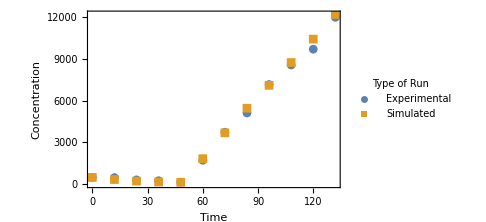

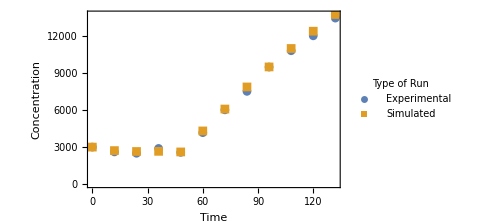

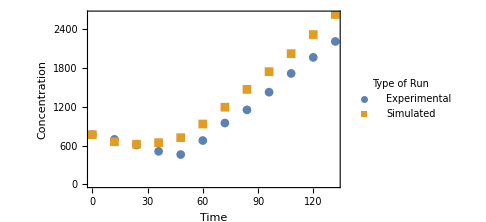

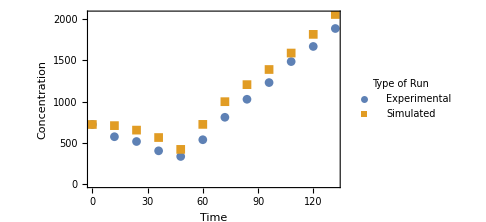

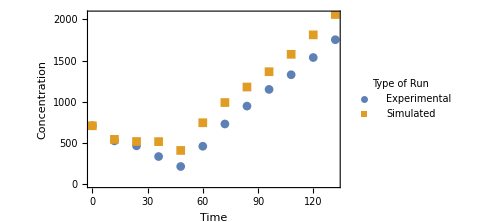

```mathematica
ListPlot[{RealNitA1,CROSSNIT8A},PlotMarkers->Automatic,Frame->True,FrameLabel->axlal,LabelStyle->Bold,PlotLegends->Placed[LineLegend[legendLab2,LegendLabel->"Type of Run",LegendFunction->(Framed[#,RoundingRadius->5]&),LabelStyle-> 10],{0.3,0.7}],ImageSize->Medium]
ListPlot[{RealNitB1,CROSSNIT8B},PlotMarkers->Automatic,Frame->True,FrameLabel->axlal,LabelStyle->Bold,PlotLegends->Placed[LineLegend[legendLab2,LegendLabel->"Type of Run",LegendFunction->(Framed[#,RoundingRadius->5]&),LabelStyle-> 10],{0.3,0.7}],ImageSize->Medium]
ListPlot[{RealNitC1,CROSSNIT8C},PlotMarkers->Automatic,Frame->True,FrameLabel->axlal,LabelStyle->Bold,PlotLegends->Placed[LineLegend[legendLab2,LegendLabel->"Type of Run",LegendFunction->(Framed[#,RoundingRadius->5]&),LabelStyle-> 10],{0.3,0.7}],ImageSize->Medium]
ListPlot[{RealNitD1,CROSSNIT8D},PlotMarkers->Automatic,Frame->True,FrameLabel->axlal,LabelStyle->Bold,PlotLegends->Placed[LineLegend[legendLab2,LegendLabel->"Type of Run",LegendFunction->(Framed[#,RoundingRadius->5]&),LabelStyle-> 10],{0.3,0.7}],ImageSize->Medium]
ListPlot[{RealNitE1,CROSSNIT8E},PlotMarkers->Automatic,Frame->True,FrameLabel->axlal,LabelStyle->Bold,PlotLegends->Placed[LineLegend[legendLab2,LegendLabel->"Type of Run",LegendFunction->(Framed[#,RoundingRadius->5]&),LabelStyle-> 10],{0.3,0.7}],ImageSize->Medium]
```

### DCW

```mathematica
(*This is plotted in regard to the cross validation data*)
```

```mathematica
(*Type 1, 1 Layer*)
```

```mathematica
legendLab2={"Experimental","Simulated"}
```

{Experimental,Simulated}

```mathematica
(*1 Hidden layer*)
```

```mathematica
(*Expected value from experimental point*)
```

```mathematica
(*Fully Simulated Trajectory*)
```

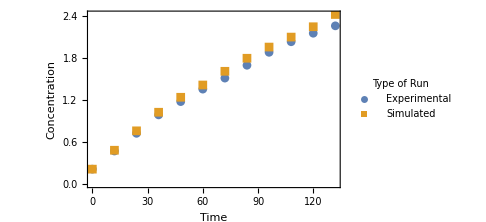

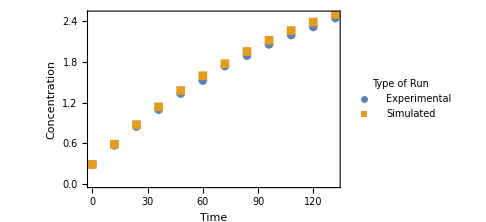

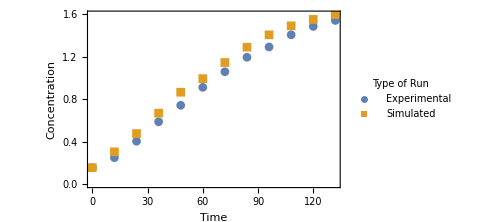

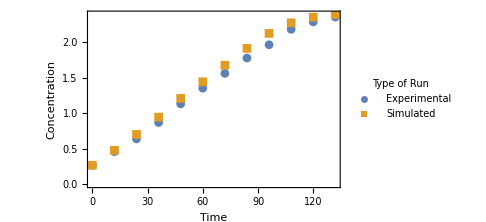

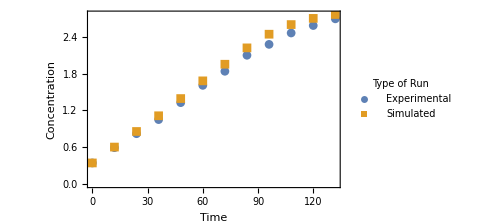

```mathematica
ListPlot[{RealDCWA1,CROSSDCW1A},PlotMarkers->Automatic,Frame->True,FrameLabel->axlal,LabelStyle->Bold,PlotLegends->Placed[LineLegend[legendLab2,LegendLabel->"Type of Run",LegendFunction->(Framed[#,RoundingRadius->5]&),LabelStyle-> 10],{0.8,0.3}],ImageSize->Medium]
ListPlot[{RealDCWB1,CROSSDCW1B},PlotMarkers->Automatic,Frame->True,FrameLabel->axlal,LabelStyle->Bold,PlotLegends->Placed[LineLegend[legendLab2,LegendLabel->"Type of Run",LegendFunction->(Framed[#,RoundingRadius->5]&),LabelStyle-> 10],{0.8,0.3}],ImageSize->Medium]
ListPlot[{RealDCWC1,CROSSDCW1C},PlotMarkers->Automatic,Frame->True,FrameLabel->axlal,LabelStyle->Bold,PlotLegends->Placed[LineLegend[legendLab2,LegendLabel->"Type of Run",LegendFunction->(Framed[#,RoundingRadius->5]&),LabelStyle-> 10],{0.8,0.3}],ImageSize->Medium]
ListPlot[{RealDCWD1,CROSSDCW1D},PlotMarkers->Automatic,Frame->True,FrameLabel->axlal,LabelStyle->Bold,PlotLegends->Placed[LineLegend[legendLab2,LegendLabel->"Type of Run",LegendFunction->(Framed[#,RoundingRadius->5]&),LabelStyle-> 10],{0.8,0.3}],ImageSize->Medium]
ListPlot[{RealDCWE1,CROSSDCW1E},PlotMarkers->Automatic,Frame->True,FrameLabel->axlal,LabelStyle->Bold,PlotLegends->Placed[LineLegend[legendLab2,LegendLabel->"Type of Run",LegendFunction->(Framed[#,RoundingRadius->5]&),LabelStyle-> 10],{0.8,0.3}],ImageSize->Medium]
```

```mathematica
(*2 Hidden Layers*)
```

```mathematica
(*Fully Simulated Trajectory*)
```

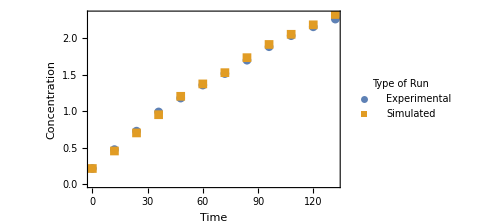

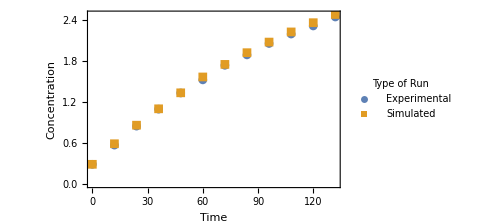

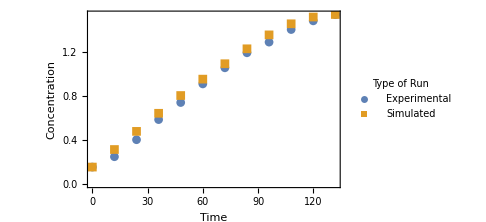

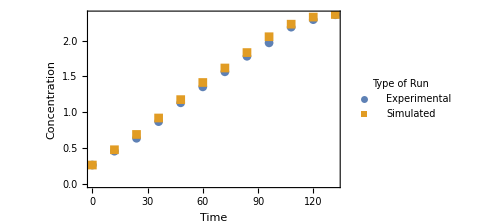

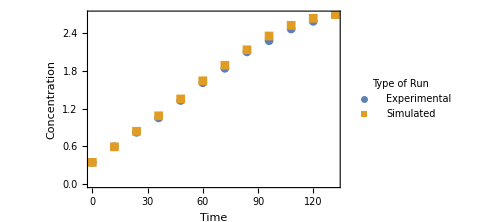

```mathematica
ListPlot[{RealDCWA1,CROSSDCW8A},PlotMarkers->Automatic,Frame->True,FrameLabel->axlal,LabelStyle->Bold,PlotLegends->Placed[LineLegend[legendLab2,LegendLabel->"Type of Run",LegendFunction->(Framed[#,RoundingRadius->5]&),LabelStyle-> 10],{0.8,0.3}],ImageSize->Medium]
ListPlot[{RealDCWB1,CROSSDCW8B},PlotMarkers->Automatic,Frame->True,FrameLabel->axlal,LabelStyle->Bold,PlotLegends->Placed[LineLegend[legendLab2,LegendLabel->"Type of Run",LegendFunction->(Framed[#,RoundingRadius->5]&),LabelStyle-> 10],{0.8,0.3}],ImageSize->Medium]
ListPlot[{RealDCWC1,CROSSDCW8C},PlotMarkers->Automatic,Frame->True,FrameLabel->axlal,LabelStyle->Bold,PlotLegends->Placed[LineLegend[legendLab2,LegendLabel->"Type of Run",LegendFunction->(Framed[#,RoundingRadius->5]&),LabelStyle-> 10],{0.8,0.3}],ImageSize->Medium]
ListPlot[{RealDCWD1,CROSSDCW8D},PlotMarkers->Automatic,Frame->True,FrameLabel->axlal,LabelStyle->Bold,PlotLegends->Placed[LineLegend[legendLab2,LegendLabel->"Type of Run",LegendFunction->(Framed[#,RoundingRadius->5]&),LabelStyle-> 10],{0.8,0.3}],ImageSize->Medium]
ListPlot[{RealDCWE1,CROSSDCW8E},PlotMarkers->Automatic,Frame->True,FrameLabel->axlal,LabelStyle->Bold,PlotLegends->Placed[LineLegend[legendLab2,LegendLabel->"Type of Run",LegendFunction->(Framed[#,RoundingRadius->5]&),LabelStyle-> 10],{0.8,0.3}],ImageSize->Medium]
```